## Functions

### Utility

```mathematica
FrontEndExecute[FrontEnd`AddMenuCommands["DuplicatePreviousOutput",{Delimiter,MenuItem["Delete cell",FrontEnd`KernelExecute[Module[{nb},nb=SelectedNotebook[];
SelectionMove[nb,Previous,Cell];
SelectionMove[nb,Next,Cell];
NotebookDelete[nb];
SelectionMove[nb,Next,Cell]]],MenuKey["k",Modifiers->{"Command"}],System`MenuEvaluator->Automatic]}]]
```

```mathematica
LocationDifferences[arr1_, arr2_, levelspec_:2] := Position[MapThread[{#1, #2} &, {arr1, arr2}, 2], {x_, y_} /; x != y, levelspec]
```

### Perturbation Viz

```mathematica
TrimArray[arr_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ arr,{}];
    If[ranges == {}, Return[arr]];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[Max[1, left-width] ;; Min[Length[arr[[1]]], right+width]]] & /@ arr,
    arr
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
ClearAll@PlotCA
```

```mathematica
Options[PlotCA] = {ColorRules -> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, "Trim" -> {1, None}, 
Mesh->False, MeshStyle -> Opacity[0.1]};
PlotCA[ca_, ops:OptionsPattern[]] := With[{allops = Merge[{Options[PlotCA],ops},Last]},
 ArrayPlot[TrimArray[ca, allops["Trim"]], ##]&[FilterRules[Normal[allops], Options[ArrayPlot]]]]

PlotCA[{ruleidx_Integer, k_Integer, r_Integer}, ops:OptionsPattern[]] :=  
With[{allops = Merge[{{"init"->{{1}, 0},"steps"->{100, All}},ops},Last]},
PlotCA[#, Sequence@@Normal[allops]]&[
CellularAutomaton[{ruleidx, k, r}, allops["init"], allops["steps"]]
]]
```

```mathematica
ClearAll@getca
```

```mathematica
getca[ru_, steps_:100, width_:All]:= CellularAutomaton[ru, {{1}, 0}, {steps, width}]
```

```mathematica
ClearAll@PlotDifferences
```

```mathematica
Options[PlotDifferences] = { 
ColorRules -> Join[{0 -> White, -100 -> GrayLevel[.8]}, 
 {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :> Lighter[#2, .7] & @@@ {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
PlotDifferences[arr1_, arr2_, ops:OptionsPattern[]] := 
Module[{locs, vals, rus, highlighted, trimmed, colrules, allops},
	allops=Merge[{Join[Options[PlotCA], Options[PlotDifferences]],ops},Last];
    locs = LocationDifferences[arr1, arr2];
    vals = arr2[[#1, #2]] & @@@ locs;
    rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
    highlighted = ReplacePart[arr1, rus];
    trimmed = TrimArray[highlighted, allops["Trim"]];
    ArrayPlot[trimmed, ##]&[FilterRules[Normal[allops], Options[ArrayPlot]]]
    ]
```

```mathematica
ClearAll@HighlightPerturbations
```

```mathematica
Options[HighlightPerturbations] = {ColorRules->Join[{100->Black},
    #1 -> GrayLevel[0.9] & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 -> #2& @@@ {0->GrayLevel[1],1->RGBColor[1, 0, 0],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
HighlightPerturbations[ca_, ops:OptionsPattern[]]:= Module[{locs, rus, 
highlighted, trimmed, allops},
allops=Merge[{Options[HighlightPerturbations],ops},Last];
locs = Position[ca, perturb[_, _]];
rus = ReplaceAll[#->-ca[[#[[1]], #[[2]], 2]]&/@ locs, 0:>100];
highlighted = ReplacePart[ca,rus];
PlotCA[highlighted, Sequence@@Normal[allops]]
]
```

### Perturbation Function

#### Low level

```mathematica
perturb = Symbol["perturb"];
```

```mathematica
ClearAll@nonzeroRange
```

```mathematica
nonzeroRange[list_]:= SparseArray[list]["NonzeroPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
getbodyidxs[ca_]:= Block[{ranges =DeleteCases[nonzeroRange/@ ca, {}]},
Table[{i, #}&/@ Range@@ranges[[i]], {i, Length[ranges]}]
]
```

```mathematica
ClearAll@getbodyrules
```

```mathematica
getbodyrules[ca_, pertbitfunc_:"Random"]:=
Module[{ranges=DeleteCases[nonzeroRange/@ca,{}]},
Flatten[Table[With[{count=Subtract@@Reverse[ranges[[i]]]+1},
Table[i->{{j},"Enumerate", pertbitfunc},{j,count}]],{i,Length[ranges]}]]]
```

```mathematica
getcoloridxs[ca_]:= 
GatherBy[SparseArray[ca]["NonzeroPositions"], First]
```

```mathematica
getflatcoloridxs[ca_]:= SparseArray[ca]["NonzeroPositions"]
```

```mathematica
ClearAll@getcolorrules
```

```mathematica
getcolorrules[ca_, pertbitfunc_:"Random"]:= Flatten[MapIndexed[#1[[1]]->{#2, "Enumerate", pertbitfunc}&, #]&/@getcoloridxs[ca]]
```

```mathematica
inrange[idxs_, range_ : {1}] := idxs[[Select[range, # >= -Length[idxs] && # <= Length[idxs] &]]]
```

```mathematica
tofunc[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  ((perturb[#, i] &) /@ # &),
   Rule["AddValue", i_Integer] :> ((perturb[#, Mod[(# + i), k]] &) /@ # &),
   "Random" :> ((perturb[#, RandomChoice[Complement[Range[0, k - 1], {#}]]] &) /@ # &),
   f_ :> (f[#, k]&)
   }]
```

```mathematica
tofunc2[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  (Table[i, Length[#]] &),
   Rule["AddValue", i_Integer] :> ((Mod[(# + i), k] &) /@ # &),
   "Random" :> ((RandomChoice[Complement[Range[0, k - 1], {#}]] &) /@ # &),
   f_ :> (f[#, k]&)
   }]
```

```mathematica
expandrange[range_, n_] := ReplaceAll[
  Replace[range, 
   {(i_Integer) :> If[i >= 1, Range[i], Range[-1, i, -1]],
    List[i_Integer, o__] :> {If[i >= 1, Range[i], Range[-1, i, -1]], o}}],
  {All :> Range[n], {{s_Integer, e_Integer}} :> Range[s, e]}
  ]
```

```mathematica
tofullform[colspec_] :=
 Replace[colspec, {
   {js__Integer} :> {{js}, "Random", "Random"},
   {{js__Integer}, s_String} :> {{js}, s, "Random"},
   {{js__Integer}, s_String, f_} :> {{js}, s, f}}]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

#### High level

```mathematica
MarkRowPerturbations[row_, colspec_, k_ : 3, r_ : 1] := Module[{coloridxs, range, 
order, bitfunc, sorted, incolorrange, pertbitfunc, vals},
  coloridxs = Replace[nonzeroRange[row], {{} :> {}, g_ :> Range @@ g}];
  {range, order, bitfunc} = tofullform[expandrange[colspec, Length[coloridxs]]];
  sorted = If[order === "Random", RandomSample[coloridxs, UpTo@Length[range]], coloridxs];
  incolorrange = sorted[[Select[range, # >= -Length[sorted] && # <= Length[sorted] &]]];
  pertbitfunc = tofunc[bitfunc, k];
  vals = pertbitfunc[row[[incolorrange]]];
  ReplacePart[row, MapThread[#1 -> #2 &, {incolorrange, vals}]]
  ]
```

```mathematica
MarkPerturbations[{ca_, {n_, k_, r_}}, pertspec_] := 
 {ReplacePart[ca, pertspec[[1]] -> MarkRowPerturbations[ca[[pertspec[[1]]]], pertspec[[2]], k, r]],
  {n, k, r}}
```

```mathematica
ClearAll@MarkPerturbationsByIndex
```

```mathematica
MarkPerturbationsByIndex[{ca_, {n_, k_, r_}}, {idxs_, pertbitfunc_}] := Module[{},
  {ReplacePart[ca, MapThread[#1 -> #2 &, {idxs, pertbitfunc[Flatten[ca[[#1, #2]] & @@@ idxs], k]}]], {n, k, r}}
  ]
```

```mathematica
ClearAll@EvolvePerturbedCA
```

```mathematica
EvolvePerturbedCA[{pca_, rule_}] := Module[{pidxs, pidx, prowidx, pre, prow, evolvedCA},
  pidxs = Position[pca, perturb[_, _], {}];
  If[pidxs == {}, {pca, rule},
   prowidx = pidxs[[1, 1]];
   pre = pca[[;; prowidx - 1]];
   prow = pca[[prowidx]] /. perturb[old_Integer, new_Integer] :> new;
   evolvedCA = Join[pre, CellularAutomaton[rule, prow, Length[pca] - Length[pre] - 1]];
       {evolvedCA, rule}
   ]]
```

```mathematica
ClearAll@PerturbIndexes
```

```mathematica
PerturbIndexes[{ca_, rule_}, idxspec_] := Module[{n, k, r, tolist, idxs, bitfuncspec, byrow},
  {n, k, r} = interpretrule[rule];
  tolist = Replace[idxspec, {{i_Integer, j_Integer} :> {{i, j}}} ];
  {idxs, bitfuncspec} = If[MatchQ[tolist, List[List[_Integer, _Integer] ...]],
   {tolist, "Random"}, {First[tolist], Last[tolist]}];
  byrow = {#, tofunc[bitfuncspec, k]} & /@ GatherBy[SortBy[idxs, #[[1]] &], #[[1]] &];
  Fold[EvolvePerturbedCA[Sow[MarkPerturbationsByIndex[#1, #2]]] &, {ca, {n, k, r}}, byrow]
  ]
```

```mathematica
PerturbIndexesFast[{ca_, rule_}, idxs_:"Random", bitfunc_:"Random"] := Module[{n, k, r,  fidxs, row, vals, newrow, pre},
  {n, k, r} = interpretrule[rule];
  fidxs = If[
    idxs === "Random", RandomSample[getflatcoloridxs[ca], 1], idxs];
  row = ca[[rowidx = fidxs[[1, 1]]]];
  vals  = tofunc2[bitfunc, k][row[[fidxs[[All, 2]]]]];
  newrow = ReplacePart[row, MapThread[#1 -> #2 &, {fidxs[[All, 2]], vals}]];
  pre = ca[[;; rowidx - 1]];
  Join[pre, CellularAutomaton[rule, newrow, Length[ca] - Length[pre] - 1]]
  ]
```

```mathematica
MarkPerturbationsByIndex[{ca_, {n_, k_, r_}}, {idxs_, pertbitfunc_}] := Module[{},
  {ReplacePart[ca, MapThread[#1 -> #2 &, {idxs, pertbitfunc[Flatten[ca[[#1, #2]] & @@@ idxs], k]}]], {n, k, r}}
  ]
```

```mathematica
PerturbCAFast[{ca_, rule_}, rowspec_ -> colspec_, lt_:-1] := Module[{n, k, r, row, rowidx, coloridxs, range, 
   order, bitfunc,topert, pertbitfunc, vals, newrow, pre},
{n, k, r} = interpretrule[rule];
 row = If[rowspec === "Random",
ca[[rowidx = RandomInteger[{1, If[lt == -1, TestCALifeTime[ca] /. -Infinity :> Length[ca], lt]}]]], 
ca[[rowidx = rowspec]]];
coloridxs = If[Length[#] > 0, Range @@ #, #]&@nonzeroRange[row];
{range, order, bitfunc} = tofullform[expandrange[colspec, Length[coloridxs]]];topert = If[order === "Enumerate", coloridxs[[range]], RandomSample[coloridxs, UpTo@Length[range]]];pertbitfunc = tofunc2[bitfunc, k];
    vals = pertbitfunc[row[[topert]]];
newrow = ReplacePart[row, MapThread[#1 -> #2 &, {topert, vals}]];
pre = ca[[;; rowidx - 1]];
     Join[pre, CellularAutomaton[rule, newrow, Length[ca] - Length[pre] - 1]]
    ]
```

```mathematica
ClearAll@PerturbCA
```

```mathematica
PerturbCA[{ca_, rule_}, pertspec_ : "Random"] := Module[{rand, torand, tolist},
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, r_Rule :> {r}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, rule}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, rule}, tolist][[1]]]
  ]
```

```mathematica
PerturbCA[{n_Integer, k_Integer, r_?NumberQ}, init_:{{1}, 0}, steps_Integer:100, pertspec_ : "Random"] := Module[{ca, rand, torand, tolist},
  ca = CellularAutomaton[{n, k, r}, init, {steps, All}]; 
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, ru_Rule :> {ru}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, {n, k, r}}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, {n, k, r}}, tolist]][[1]]
  ]
```

```mathematica
ClearAll@PerturbedCAEvolution
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_ : 100, pertspec_ : "Random"] := 
  Module[{ca = CellularAutomaton[rule, init, {steps, All}]},
  Replace[pertspec,
   {
    ("Random" | _Integer | _Rule | {_Integer, _Integer} | {_Rule ..} | {{_Integer, _Integer} .. } 
    | {{{_Integer, _Integer} ..  }, _Rule})
     :> EvolvePerturbedCA[Sow[PerturbCA[{ca, rule}, pertspec]]][[1]],
    ({{_Rule ..} ..} | {{{_Integer, _Integer} .. } ..} | {{{{_Integer, _Integer} ..  }, _Rule} ..}
     | {{{{_Integer, _Integer} ..  }, _Rule} ..})
      :> FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, #2]]] &, {ca, rule}, pertspec][[All, 1]],
    {{{{_Integer, _Integer} .. } ..}, r_Rule} :> 
    FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, {#2, r}]]] &, {ca, rule}, First[pertspec]][[All, 1]]
      }
        ]]
```

### Analysis Functions

```mathematica
ClearAll@CountSame
```

```mathematica
CountSame[arr1_, arr2_]:= Block[{sa},sa = SparseArray[arr1-arr2]; Times@@Dimensions[sa] - Length[sa["NonzeroValues"]]]
```

```mathematica
CountDifferences[arr1_,arr2_]:=Length[SparseArray[arr1-arr2]["NonzeroValues"]]
```

```mathematica
TestCALifeTime[ca_]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
PerturbationSensitivity[{ca_, ru_}, pertspec_:("Random"->1), lt_:-1]:= 
With[{clt =If[lt== -1, TestCALifeTime[ca], lt] },
 Abs[
clt - TestCALifeTime[PerturbCAFast[{ca, ru}, pertspec]]]//If[#==Infinity, Max[clt,Length[ca] - clt], #]&
]
```

```mathematica
PerturbationSensitivity2[{ca_, ru_}, pertspec_:("Random"->1), lt_:-1]:= 
With[{clt =If[lt== -1, TestCALifeTime[ca], lt] },
TestCALifeTime[PerturbCAFast[{ca, ru}, pertspec]] - clt//If[#==-Infinity, Length[ca] - clt, #]&
]
```

```mathematica
PerturbationSensitivities3[{pat, ru}]
```

{-118,-63,-104,-116,-4,3,-40,-108,-61,-101,7,2,2,0,3,-110,5,4,-110,-58,2,-102,-102,-102,2,11,6,74,-55,-37,8,-46,-9,-55,-94,-55,-79,-41,-93,19,-94,-94,83,-97,66,10,83,-55,83,-100,-91,83,10,28,-55,21,12,10,83,39,16,83,83,83,-76,20,-71,39,-78,-89,83,12,83,83,25,-88,-41,3,83,-7,0,25,83,-89,18,0,-30,83,41,83,12,35,25,19,83,41,33,12,83,60,25,-91,-38,-35,41,31,44,83,-85,-84,22,83,-43,12,-73,83,-12,19,31,-30,4,3,-43,24,0,-82,83,-5,31,40,9,54,-43,-76,-57,0,32,83,83,83,81,48,83,-43,83,61,33,43,83,33,22,48,-43,83,-44,-27,61,83,33,83,22,83,83,83,45,-27,83,45,33,83,83,34,67,83,83,83,83,45,14,83,25,61,3,34,83,75,83,83,83,83,83,83,83,83,83,83,83,-70,83,83,83,44,83,83,83,83,-7,-12,57,0,49,83,1,1,48,83,83,15,83,83,83,83,83,83,66,83,83,-34,83,36,67,83,57,83,49,83,83,83,39,83,83,0,83,83,46,55,64,83,83,83,83,49,34,83,83,67,83,83,83,83,19,-70,-62,83,67,54,83,83,83,82,38,83,83,-70,83,52,83,83,-34,54,83,83,83,29,83,83,83,83,0,-62,83,83,83,83,0,28,83,83,83,41,82,83,72,36,43,42,58,-62,83,83,83,83,83,55,19,52,-27,48,43,57,-22,83,0,-62,0,83,-21,83,83,83,83,83,-12,52,83,83,-61,-22,-62,83,0,0,83,83,83,35,-47,46,4,83,83,-54,41,4,-38,0,83,53,83,83,0,-53,83,83,-56,-18,0,-48,-62,83,83,0,83,9,83,57,83,83,-48,60,-62,-62,83,-60,83,-56,83,0,0,0,0,83,27,0,83,83,57,83,-62,41,-4,-55,83,83,0,83,0,0,0,83,76,83,83,-52,-10,83,60,-51,83,83,83,0,-52,0,83,79,-25,65,83,0,83,48,-42,48,83,-56,-60,83,58,0,1,83,0,83,69,83,49,49,83,63,41,61,-56,83,83,46,0,83,0,83,0,0,83,0,83,83,-57,49,83,83,-53,52,83,83,83,83,0,0,83,83,71,83,-40,66,83,0,-41,41,49,-62,11,46,-18,0,83,0,83,0,0,-1,0,54,-57,83,58,49,49,49,83,83,51,83,83,0,83,83,83,83,54,-56,-57,0,0,83,48,49,0,83,0,83,83,83,83,-16,34,-57,-57,-57,55,0,83,49,-61,83,0,83,0,0,83,69,-49,49,-57,83,83,-2,83,-52,52,-18,0,0,83,83,5,59,-24,-49,-16,-9,-50,20,83,83,-52,83,26,11,0,0,83,0,83,83,83,69,49,52,-50,-54,83,59,83,-57,83,83,0,0,0,83,83,0,65,65,83,-54,55,35,-54,83,-57,-3,83,0,83,83,0,0,-35,0,0,83,-54,52,57,18,-57,0,83,83,0,0,0,0,0,-7,52,83,38,-60,57,-55,74,-7,83,-58,-47,-57,59,83,10,83,54,57,56,83,58,83,61,-5,-18,-48,62,62,-30,62,83,61,83,62,56,68,47,83,44,77,66,83,7,66,-42,77,57,-42,-42,0,7,2,63,64,9,59,66,-49,-51,66,-39,-12,79,0,83,-43,68,-44,79,23,83,-39,83,-49,70,-39,83,-39,83,-47,81,83,70,-37,83,-41,67,67,83,32,83,69,83,27,83,83,-39,73,81,78,83,27,83,83,-38,83,72,0,83,83,-23,83,83,83,24,83,83,-31,83,17,20,83,81,83,-31,26,75,0,-16,83,5,-23,83,75,83,83,32,83,83,-23,83,-13,26,83,83,61,83,50,-13,-25,66,75,81,61,-6,83,83,83,-31,-25,83,36,83,83,44,-15,83,83,83,56,83,83,-22,-8,0,83,23,66,56,83,83,-5,83,-8,83,83,-9,-25,83,66,83,83,-8,83,83,83,83,50,23,-12,83,-24,83,83,-8,30,-1,83,83,83,83,52,83,83,83,83,30,83,83,83,33,-16,23,83,52,29,83,83,83,83,83,83,83,63,83,33,83,27,83,83,31,83,0,33,30,83,-6,83,30,31,83,83,83,0,83,83,83,55,-7,83,83,-15,40,83,83,83,83,83,56,-4,83,83,83,83,83,0,83,-2,-15,83,53,83,83,33,83,83,-2,83,83,83,83,83,33,83,83,-5,2,29,29,83,73,83,83,83,35,83,83,83,83,56,6,-15,-15,83,83,83,83,83,83,83,83,83,83,36,-10,83,83,83,83,83,83,83,83,14,36,83,83,78,-4,83,83,83,83,83,58,83,83,73,73,83,83,-2,83,83,83,56,83,43,83,-6,83,83,-2,79,83,-10,44,83,43,45,-6,44,83,83,83,44,-4,56,33,83,-9,83,-4,14,83,83,83,83,83,83,1,83,-13,83,0,83,83,14,83,83,83,-12,83,0,0,83,0,83,83,-13,0,83,83,0,83,41,-10,83,83,83,-11,0,-8,-11,-3,2,43,-7,83,6,43,83,20,83,2,83,83,83,83,6,70,83,83,83,83,83,83,1,83,19,8,9,0,5,19,83,83,-2,-1,-2,83,2,83,0,0}

```mathematica
PerturbationSensitivities[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=
PerturbationSensitivity[{ca, ru},#, lt]&/@ getbodyrules[ca, pertbitfunc]
```

```mathematica
ClearAll@PerturbationSensitivities
```

```mathematica
PerturbationSensitivities2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=
PerturbationSensitivity[{ca, ru},#, lt]&/@ getcolorrules[ca, pertbitfunc]
```

```mathematica
PerturbationSensitivities3[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=
PerturbationSensitivity2[{ca, ru},#, lt]&/@ getbodyrules[ca, pertbitfunc]
```

```mathematica
meanfragility[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
meanfragility2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities2[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
ClearAll@PerturbationSensitivityPlot
```

```mathematica
PerturbationSensitivityPlot[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getbodyidxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,
ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),
ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

```mathematica
PerturbationSensitivityPlot2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getcoloridxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities2[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

```mathematica
ClearAll@PerturbationSensitivityPlot3
```

```mathematica
PerturbationSensitivityPlot3[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= 
 Module[{idxs =Flatten[getbodyidxs[ca], 1]},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities3[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, 
ColorFunctionScaling->False,
ColorFunction->(diffblend[Replace[#, -1->0], clt, Length[ca]]&),
ColorRules->{0->White,Infinity->Red}]]]
```

```mathematica
diffblend[value_, lt_, lca_]:=
With[{diff = value + lt},
Piecewise[{(*Gradual transition from light gray to blue for values between 0 and 0.9*)
{Blend[{LightGray,Blue},diff/lt],diff<=lt},
(*Sharp transition from blue to red åfor values between 0.9 and 1*)
{Blend[{Blue, Red},value/(lca - lt)],diff>lt}}]]
```

### Adapt Therapy

TODO: make arg 11

```mathematica
AdaptTherapy[{initpat_, initru_}, {ca_, currdiff_, mca_, i_}]:= Block[{pca, nca, nmca, newdiff},
nmca = Reap[pca =PerturbCA[{ca, initru}, Floor[11+i]]][[2, 1, 1, 1]];
newdiff = CountDifferences[initpat,pca];
nca = If[newdiff<= currdiff, pca,ca];
{nca, Min[newdiff, currdiff], nmca, i+(1/5)}]
```

### Micro

```mathematica
flipall[bits_, k_]:= ((perturb[#, Complement[Range[0, k - 1], {#}]] &) /@ bits)
```

```mathematica
getperts[tup_, k_]:= Tuples[Replace[ReplacePart[tup, Ceiling[Length[tup] / 2]->Complement[Range[0, k - 1], tup[[{Ceiling[Length[tup] / 2]}]]]], i_Integer:> {i}, 1]]
```

```mathematica
getpertrus[i_, perts_]:= {i, #}&/@ perts
```

```mathematica
getsubs[{n_, k_, r_}]:= MapThread[#1->#2&, {Reverse[Tuples[Range[0, k - 1], 1 + 2r]],IntegerDigits[n, k, k^(2r+1)]}]
```

```mathematica
getpertedges[k_, r_]:= getpertrus[#, getperts[#, k]]&/@Tuples[Range[0, k - 1],4r+ 1]
```

```mathematica
getruparts[{arr1_, arr2_}, r_:1]:= Transpose[Partition[#, 2r+1, 1]&/@ {arr1, arr2}]
```

```mathematica
pertdiffs[{n_, k_, r_}]:= Block[{ruparts, stepped},
 ruparts =Map[getruparts[#, r]&, getpertedges[k, r], {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
totalpertdiffs[ru_]:= Total[pertdiffs[ru], 3]
```

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
RuleTuples[k_,r_]:=RuleTuples[k,r]=Tuples[
Reverse[Range[0,k-1]],2r+1]
```

```mathematica
RuleMask[{ru_,k_,r_},lt_]:=Module[
{data,mask,canonical},
data=Union[Catenate[Map[Partition[#,2r+1,1]&,
CellularAutomaton[{ru,k,r},
CenterArray[1,2 r*(lt+4)+1],lt+2]]]];
mask=Lookup[Association[Thread[data->1]],RuleTuples[k,r],0]
(*canonical=IntegerDigits[ru,k,Length[mask]];{
FromDigits[canonical*mask,k],
FromDigits[mask,2]
}*)
]
```

```mathematica
getruleloc[bits_, k_, r_] := FirstPosition[RuleTuples[k, r], bits][[1]]
```

```mathematica
plotrule[rule_, ops:OptionsPattern[{"Trim"->{None, None}, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
PlotCA[{digits}, "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
plotmaskedrule[rule_, ops:OptionsPattern[{"Overlap"->False,"Trim"->{None, None}, ColorRules->withmask,Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{n, k, r, mult, mask, masked,digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
mult = If[OptionValue["Overlap"], -1, 100];
mask = RuleMask[rule, TestLifetime[rule, 200]]*mult;
masked = (mask/. 0:> 1) * ReplaceAll[digits, 0:> 100];
PlotCA[If[OptionValue["Overlap"], {masked}, {digits, mask}], "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
getgenelocs[{pca_, ru_}]:= Module[{n, k, r, pidxs, windows, oldwindows, newwindows, oldrulesets, newrulesets, genepairs, locs}, 
{n, k, r} = interpretrule[ru];
pidxs = Position[pca, perturb[_,_], {}];
windows = pca[[#[[1]], #[[2]]- 2r;;#[[2]]+ 2r]]&/@ pidxs;
oldwindows = # /. perturb[old_Integer, new_Integer]:> old&/@windows;
newwindows = # /. perturb[old_Integer, new_Integer]:> new&/@windows;
oldrulesets = Partition[#, 2r+1, 1]&/@ oldwindows;
newrulesets = Partition[#, 2r+1, 1]&/@ newwindows;
genepairs = MapThread[{#1, #2}&, {oldrulesets, newrulesets}, 2];
locs = Map[getruleloc[#, k, r]&, genepairs, {3}]
]
```

```mathematica
overlaplightrules = Join[{-100 -> GrayLevel[.8]}, 
   #1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

If active lighter, if white active gray

```mathematica
overlapdarkrules =  Join[{100 -> GrayLevel[.5]}, 
   -#1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    #1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

```mathematica
withmask ={0->GrayLevel[1], 1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 100->GrayLevel[0.2]};
```

```mathematica
getmidx[x1_, x2_]:= (x1 - x2)/ 2+x2
```

```mathematica
ClearAll@getcurves
```

```mathematica
getcurves[locs_, {n_, k_, r_}, y_:2]:= Module[{withmid, pts, curves, witharrows},
digs = IntegerDigits[n, k];
cols = If[digs[[#[[1]]]] == digs[[#[[2]]]],RGBColor[0.36, 0.8300000000000001, 0], RGBColor[1., 0.63, 0.1]]&/@ Flatten[locs, 1];
withmid = Map[{#[[1]], getmidx[#[[1]], #[[2]]], #[[2]]}&, locs - 1/2, {2}];
pts = Map[{{#[[1]], y}, {#[[2]], Min[Max[(Abs[#[[3]]- #[[1]]] + 1)/2, y+3], 10]}, {#[[3]], y}} &, withmid, {2}];
curves = Flatten[Map[BezierCurve, pts, {2}], 1];
styled = MapThread[Style[#1, #2]&, {Arrow/@ curves, cols}];
Graphics[{Arrowheads[0.025],GrayLevel[0.4], styled}]
]
```

```mathematica
PerturbedRulePlot[{pca_, ru_}, ops:OptionsPattern[]]:= 
With[{allops = Merge[{"Mask"->False, ops},Last]},
If[allops["Mask"], Show[plotmaskedrule[ru],getcurves[getgenelocs[{pca, ru} ],ru, 2], Sequence@@FilterRules[Normal[allops], Options[Graphics]]], 
Show[plotrule[ru],getcurves[getgenelocs[{pca, ru}], ru, 1], Sequence@@FilterRules[Normal[allops], Options[Graphics]]]]]
```

```mathematica
activebodytups[{ca_, ru_}, tupfunc_:(4#+1&)]:= Module[{n, k, r}, 
{n, k, r} = interpretrule[ru];
lt = TestCALifeTime[ca];
bodytups = Partition[#, tupfunc[r], 1]&/@MapThread[#1[[#2[[1]] - 2r;; #2[[2]] + 2r]]&, {ca[[;;lt]], (nonzeroRange/@ca)[[;;lt]]}]]
```

```mathematica
getpertpairs[{n_, k_, r_}, active_]:= (getpertrus[#, getperts[#, k]]&/@active)
```

```mathematica
pertdiffs[{n_, k_, r_}, pertpairs_]:= Block[{},
 ruparts =Map[getruparts[#, r]&, pertpairs, {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
mask = Map[Replace[#[[1]] - #[[2]], Except[0]->1]&, stepped, {3}];
Total[mask, {3}]]
```

```mathematica
meanmicrofragility[{ca_, ru_}]:= Module[{n,k, r,counts, pd},
counts = ReverseSort[Counts[Flatten[activebodytups[{ca, ru}], 1]]];
pd = pertdiffs[ru, getpertpairs[ru, Keys[counts]]];
N@Mean[WeightedData[Mean/@ pd, Values[counts]]]
]
```

## Running Code

### Init

```mathematica
k4rob =Select[ , Last[#]>100&];
k4reg= Select[,Last[#]>100&];
```

```mathematica
psrob = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/Biomed/Output/psrob1.csv"];
```

```mathematica
msrob = N[Mean/@ psrob];
```

```mathematica
psreg = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/Biomed/Output/psreg1.csv"];
```

```mathematica
msreg = N[Mean/@ psreg];
```

```mathematica
sirob = SortBy[Range[Length[k4rob]], msrob[[#]]&];
```

```mathematica
sireg = SortBy[Range[Length[k4reg]], msreg[[#]]&];
```

```mathematica
ru = k4rob[[1, 1]];
{n, k, r} = ru;
pat = getca[ru, 200];
ca = pat;
```

### Looking For Differences in Rulesets of Robust and Regular

```mathematica
psrob = ParallelMap[PerturbationSensitivities[{getca[#, 200], #}]&,k4rob[[All, 1]]];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/Biomed/Output/psrob1.csv", psrob]
```

Projects/Wolfram/CAEvolution/Biomed/Output/psrob1.csv

```mathematica
psreg = ParallelMap[PerturbationSensitivities[{getca[#, 200], #}]&,k4reg[[All, 1]]];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/Biomed/Output/psreg1.csv", psreg]
```

Projects/Wolfram/CAEvolution/Biomed/Output/psreg1.csv

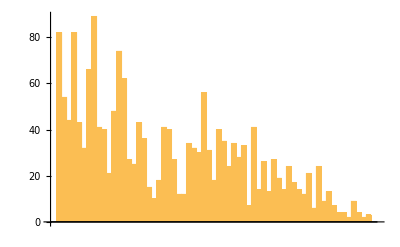
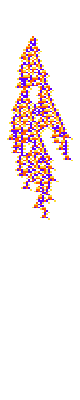
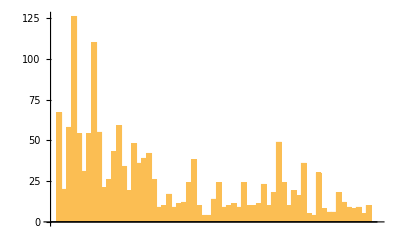
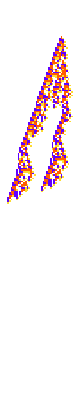
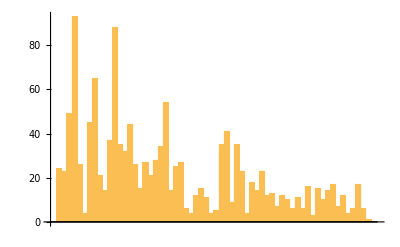
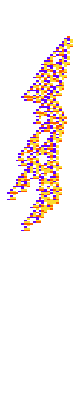
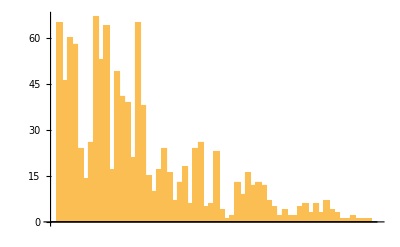
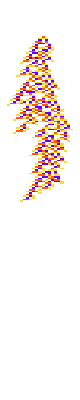
{{3.74071,-Graphics-,-Graphics-},{8.73206,-Graphics-,-Graphics-},{7.06086,-Graphics-,-Graphics-},{3.3848,-Graphics-,-Graphics-},{3.56846,-Graphics-,-Graphics-},{5.73383,-Graphics-,-Graphics-},{5.28263,-Graphics-,-Graphics-},{4.16212,-Graphics-,-Graphics-},{5.09219,-Graphics-,-Graphics-},{6.053,-Graphics-,-Graphics-},{12.1876,-Graphics-,-Graphics-},{6.45323,-Graphics-,-Graphics-},{8.38671,-Graphics-,-Graphics-},{16.2199,-Graphics-,-Graphics-},{50.8775,-Graphics-,-Graphics-},{5.71516,-Graphics-,-Graphics-},{5.44209,-Graphics-,-Graphics-},{6.13954,-Graphics-,-Graphics-},{5.59741,-Graphics-,-Graphics-},{3.56407,-Graphics-,-Graphics-},{5.21789,-Graphics-,-Graphics-},{4.21862,-Graphics-,-Graphics-},{8.74372,-Graphics-,-Graphics-},{7.77207,-Graphics-,-Graphics-},{5.37452,-Graphics-,-Graphics-},{5.75542,-Graphics-,-Graphics-},{6.74475,-Graphics-,-Graphics-},{7.20214,-Graphics-,-Graphics-},{5.0596,-Graphics-,-Graphics-},{5.19151,-Graphics-,-Graphics-}}

```mathematica
(CompoundExpression[
rcs = Rest[Counts[Catenate[Partition[#,3,1]&/@ getca[#, 200]]]],{N@Kurtosis[rcs],BarChart[rcs],PlotCA[#, "steps"->200]} ]&/@ k4rob[[All, 1]])[[sirob]]
```

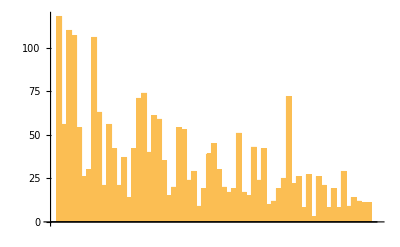
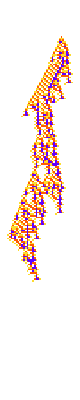
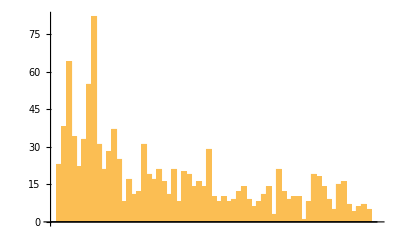
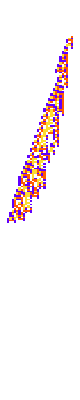
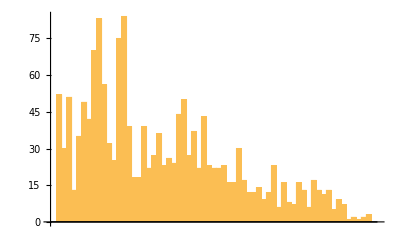
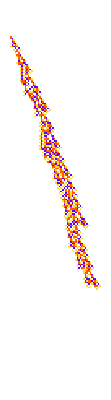
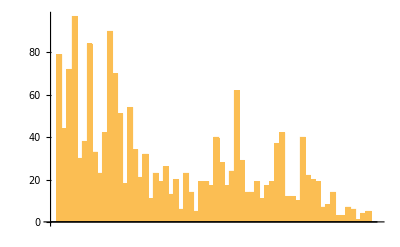
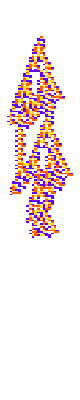
{{4.65588,-Graphics-,-Graphics-},{9.69602,-Graphics-,-Graphics-},{4.20089,-Graphics-,-Graphics-},{4.46935,-Graphics-,-Graphics-},{3.38154,-Graphics-,-Graphics-},{5.81783,-Graphics-,-Graphics-},{7.536,-Graphics-,-Graphics-},{4.72135,-Graphics-,-Graphics-},{2.97853,-Graphics-,-Graphics-},{6.08204,-Graphics-,-Graphics-},{4.79003,-Graphics-,-Graphics-},{17.627,-Graphics-,-Graphics-},{7.84344,-Graphics-,-Graphics-},{4.00454,-Graphics-,-Graphics-},{5.85367,-Graphics-,-Graphics-},{4.91554,-Graphics-,-Graphics-},{4.55975,-Graphics-,-Graphics-},{7.32143,-Graphics-,-Graphics-},{4.99818,-Graphics-,-Graphics-},{3.90784,-Graphics-,-Graphics-},{5.95024,-Graphics-,-Graphics-},{5.42589,-Graphics-,-Graphics-},{5.11563,-Graphics-,-Graphics-},{2.5131,-Graphics-,-Graphics-},{6.16491,-Graphics-,-Graphics-},{5.77862,-Graphics-,-Graphics-},{4.3378,-Graphics-,-Graphics-},{9.47384,-Graphics-,-Graphics-},{12.9095,-Graphics-,-Graphics-},{5.23016,-Graphics-,-Graphics-}}

```mathematica
(CompoundExpression[
rcs = Rest[Counts[Catenate[Partition[#,3,1]&/@ getca[#, 200]]]],{N@Kurtosis[rcs],BarChart[rcs],PlotCA[#, "steps"->200]} ]&/@ k4reg[[All, 1]])[[sireg]]
```

### Carefully Observing Perturbation Effect of Robust Rules

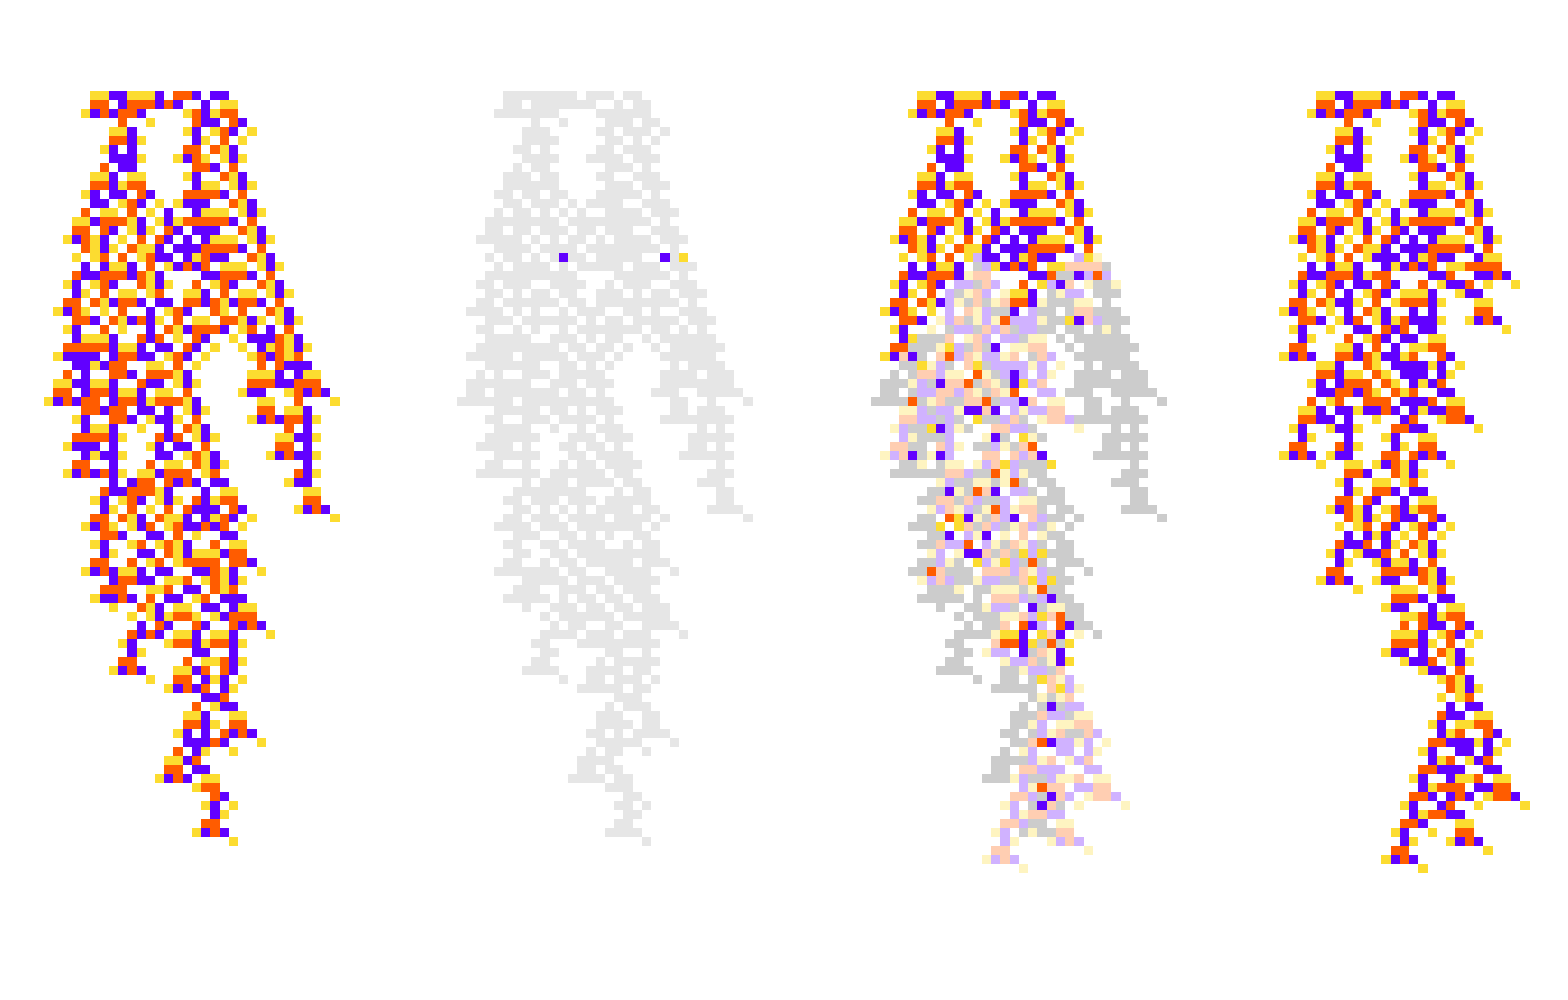

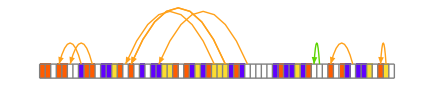

```mathematica
span = 30;;120;
ru = k4rob[[sirob[[1]], 1]];
ca =getca[ru, 200];
pru = 35->{RandomSample[Range[4, 7, 1], 1], "Enumerate"};
marked = Reap[pca = PerturbCA[{ca, ru}, "Random"->3]][[2, 1,1, 1]];
GraphicsRow[{PlotCA[ca[[span]], ImageSize->Small], HighlightPerturbations[marked[[span]], ImageSize->Small], PlotDifferences[ca[[span]], pca[[span]], ImageSize->Small], PlotCA[pca[[span]], ImageSize->Small]}]
PerturbedRulePlot[{marked, ru}]
```

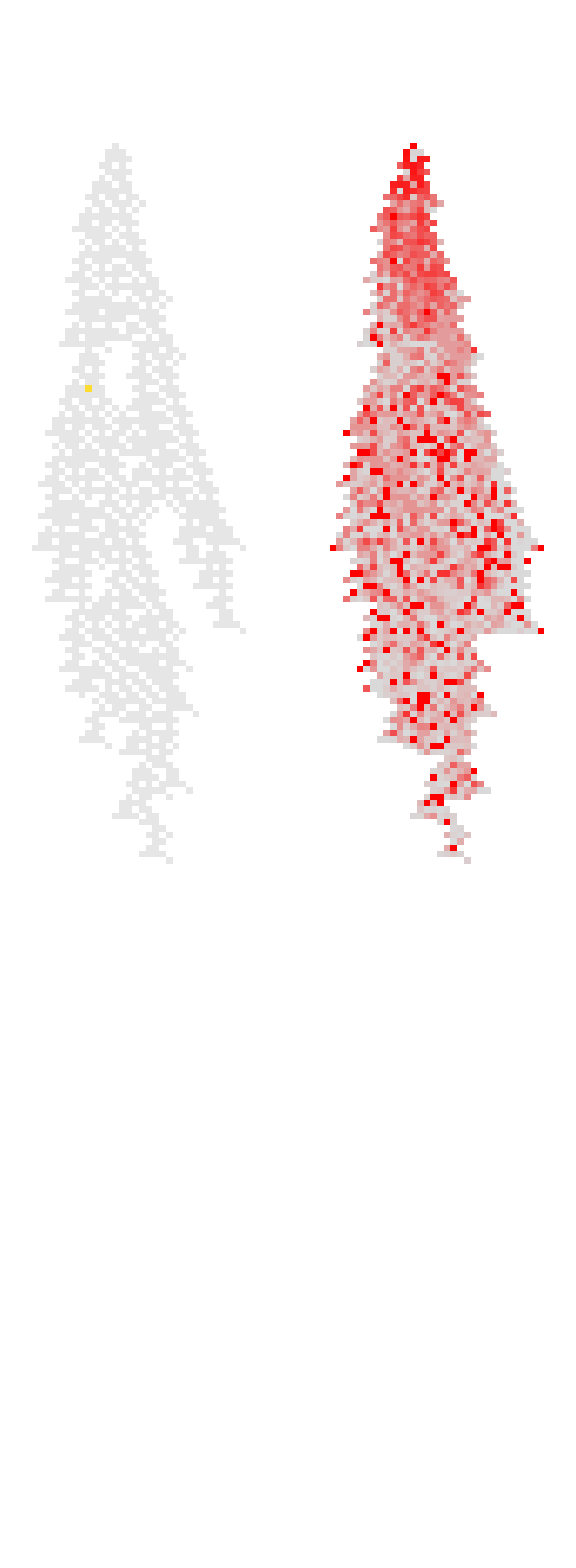

```mathematica
GraphicsRow[{HighlightPerturbations[MarkPerturbations[{ca, ru}, pru][[1]]], sp}, ImageSize->Large]
```

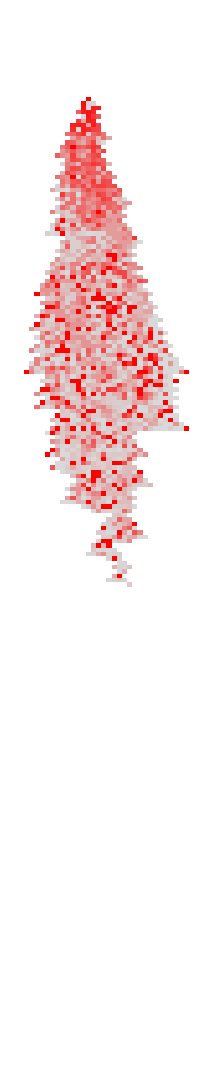

```mathematica
sp = PerturbationSensitivityPlot[{ca, ru}]
```

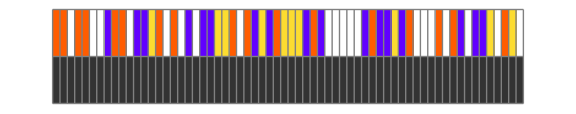

```mathematica
plotmaskedrule[ru, ImageSize->Large]
```

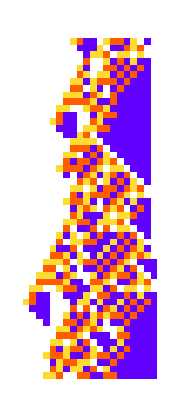
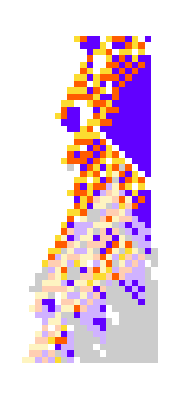
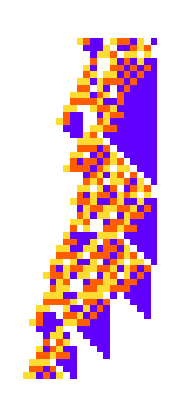
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ru = k4reg[[sirob[[4]], 1]];
ca =getca[ru, 200];
marked = Reap[pca = PerturbCA[{ca, ru}, 50->{RandomSample[Range[10], 2],"Enumerate", "SetValue"->0}]][[2, 1,1, 1]];
{PlotCA[ca[[30;;80]], ImageSize->Small], HighlightPerturbations[marked[[30;;80]], ImageSize->Small], PlotDifferences[ca[[30;;80]], pca[[30;;80]], ImageSize->Small], PlotCA[pca[[30;;80]], ImageSize->Small]}
```

```mathematica
meanfragility[{ca, ru}] // N
```

145.184

```mathematica
PlotCA/@k4reg[[;;10, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Measuring Fragility of Robust and Regular Genomes

#### On all tuples

```mathematica
totalpertdiffs/@ k4reg[[All, 1]] //Histogram[#, 10,PlotRange->{Automatic, 0}]&
```

-Graphics-

```mathematica
Length[k4reg]
```

30

```mathematica
totalpertdiffs/@ k4rob[[All, 1]]  //Histogram[#, 10, PlotRange->All]&
```

-Graphics-

#### On active tuples

Find active tuples

```mathematica
ClearAll@activetups
```

```mathematica
activetups[{ca_, ru_}]:= Module[{n, k, r}, 
{n, k, r} = interpretrule[ru];
Counts[Flatten[Partition[#, 4r+1, 1]&/@ ca, 1]]]
```

```mathematica
activebodytups[{ca_, ru_}]:= Module[{n, k, r}, 
{n, k, r} = interpretrule[ru];
lt = TestCALifeTime[ca];
bodytups = Partition[#, 4r+1, 1]&/@MapThread[#1[[#2[[1]] - 2r;; #2[[2]] + 2r]]&, {ca[[;;lt]], (nonzeroRange/@ca)[[;;lt]]}]]
```

```mathematica
ClearAll@getpertpairs
```

```mathematica
getpertpairs[{n_, k_, r_}, active_]:= (getpertrus[#, getperts[#, k]]&/@active)
```

```mathematica
pertdiffs[{n_, k_, r_}, pertpairs_]:= Block[{},
 ruparts =Map[getruparts[#, r]&, pertpairs, {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
perts  = getpertedges[ru, at];
```

Range::range: Range specification in Range[0,338187752578020983452218514940404460855] does not have appropriate bounds.

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[{Range[0,338187752578020983452218514940404460855],{0,1,2,3},{0}},1+4 activetups[{{{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},{0,0,0,0,0,0,0,0,0,0,«391»},«191»},{«1»}}]].

Range::range: Range specification in Range[0,338187752578020983452218514940404460855] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 2 in Complement[{Range[0,338187752578020983452218514940404460855],{0,1,2,3},{0}},1].

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[{{{Range[0, 338187752578020<<15>>404460855], <<2>>}, {<<3>>}}, <<3>>}, {<<4>>}].

```mathematica
undir = Map[#[[1]]->#[[2]]&, perts, {2}];
```

```mathematica
styled  = 
MapThread[Style[#1, #2]&, {undir,Map[If[Total[#, 2]== 0, RGBColor[0.36, 0.8300000000000001, 0], LightGray]&,pertdiffs[ru, at], {2}]}, 2];
```

TODO: Separate subgraphs and then plot the subgraphs according to size or something use that function that makes a table out of a list and then do a graphics column of that. Vertex size should also correspond to that in case you have a group of 5. Edges should be styled by their differences with the most healthy being green and the least healthy being a light gray. Or maybe doing red to green could make sense. But presumably there will be cases where a very frequent rule when perturbed leads to an infrequent one, in that case it would suit the automata to match the less frequent one to the more frequent one. Then you can try to minimize the weighted fragility of you’re genome and this is basically diploidism. Where you have multiple different genes doing the same function. If one gene goes bad

You should look what happens if you perturb the genome of a robust automata to see how genetically robust these things are and if it is possible to stay at the same lifetime, then you’d want to see what happens if you switch on and off those genes to see if you can get more robustness, also just looking at minimizing the weighted robustness would be good, and then seeing what you get on the random perturbation side.

You can also categorize the types of robustness observed, redundancy, protective tissue, and also irreducible robustness.

```mathematica
UndirectedGraph[Catenate[MapThread[Style[#1, #2]&, {pe,Map[If[Total[#, 2]== 0, RGBColor[0.36, 0.8300000000000001, 0], RGBColor[1., 0.63, 0.1]]&,pertdiffs[ru, at], {2}]}, 2]],EdgeStyle->White(*Opacity[.4]*),VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->20, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}, GraphLayout->"LayeredDigraphEmbedding"]
```

Without plots

With edge styles

```mathematica
styles = If[]
```

### Continuing weighted robustness plot

```mathematica
ru
PlotCA[pat, "steps"->200]
```

{148929425018041907435018990866096194332,4,1}

-Graphics-

```mathematica
ClearAll@PerturbationSensitivityGraph
```

```mathematica
PerturbationSensitivityGraphs[{ca_, ru_}, size_:1]:= Module[{counts =Rest[Counts[Sort[Flatten[activebodytups[{ca, ru}], 1]]]]*size },
pairs = getpertpairs[ru,Keys[counts]];
diffs = pertdiffs[ru,pairs];
edges = Map[#[[1]]->#[[2]]&, pairs, {2}];
cols = Map[Replace[#, {0:>RGBColor[0, 0.77, 0],1:>RGBColor[0.88, 0.84, 0], 2:> Orange,3:> Red}]&, diffs, {2}];
styled  = 
MapThread[Style[#1,#2 ]&, {edges,cols}, 2];
cg = WeaklyConnectedGraphComponents[Flatten[styled]];
cgs = ReverseSortBy[cg, Total[counts[#]&/@EdgeList[#][[All, 1]]]&];
gps = With[{cw =Total[counts[#]&/@EdgeList[#][[All, 1]]], vws =#->counts[#]/20&/@VertexList[#]}, GraphPlot[#,(*GraphLayout->"LayeredDigraphEmbedding",*)ImageSize->cw*.75,EdgeShapeFunction->{{"FilledArrow"},(Style[Arrow[#1],Arrowheads[counts[#2[[1]]]/200], Thickness[(counts[#2[[1]]]/(cw*5))]]&)}, VertexLabels->{x_/;counts[x]>=8:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->1.25counts[x], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}]]&/@ cgs;
Multicolumn[gps, {Automatic, Floor[Length[counts]/12]}]
]
```

```mathematica
PerturbationSensitivityGraph[{pat, ru}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |

#### Making bar chart version

```mathematica
Options[PerturbationSensitivityChart] = {"NumBars"->100, "ShowSequences"->False};
PerturbationSensitivityChart[{ca_, ru_}, OptionsPattern[PerturbationSensitivityChart]]:= Module[{counts =Rest[Counts[Sort[Flatten[activebodytups[{ca, ru}], 1]]]], n, k, r},
{n, k, r} = interpretrule[ru];
pp = getpertpairs[ru,Keys[ReverseSort[counts]]];
pd = pertdiffs[ru,pp];
withcols =  MapThread[Style[#1, Blend[{RGBColor[0, 0.77, 0],RGBColor[0.88, 0.84, 0], Orange,Red},Total[#2]/((k - 1) * (2r+1))]]&, {Values[ReverseSort[counts]], pd}][[;;UpTo[Replace[OptionValue["NumBars"], All:> Length[pd]]]]];
labfunc = If[OptionValue["ShowSequences"], (Placed[PlotCA[Transpose@{Keys[ReverseSort[counts]][[#2[[2]]]]}, ImageSize->{20, 30}],Below]&), Automatic];
BarChart[withcols, LabelingFunction-> labfunc]]
```

```mathematica
PerturbationSensitivityChart[{pat, ru}(*, "NumBars"->All*)]
```

-Graphics-

### Evolving Robust Rules To Even More Robust

#### #1

```mathematica
PlotCA[k4reg[[4, 1]]]
```

-Graphics-

```mathematica
evo48 = Module[
{steps = 1000,cut=200,lt, ca ,mf, nru},
SeedRandom[426750];
evo=NestList[CompoundExpression[
nru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[nru, 200];lt = TestCALifeTime[ca];
If[lt < initlt, #,{nru, lt}
(*mf = meanfragility[{ca, nru}];
If[mf<=Last[#],{nru,lt, mf},#]*)
]]&,{k4reg[[1]], 150(*, initmf*)},steps]
];
```

```mathematica
evo48[[All, 2]]
```

{150,150,150,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199,199}

```mathematica
PlotCA[#[[1, 1]], "steps"->200]&/@SplitBy[evo48,#[[2]]&]
```

{-Graphics-,-Graphics-}

```mathematica
PerturbationSensitivityPlot[{getca[evo48[[-1, 1]], 200], evo48[[-1, 1]]}]
```

-Graphics-

```mathematica
meanfragility@{getca[evo48[[-1, 1]], 200], evo48[[-1, 1]]} // N
```

141.489

```mathematica
N@%
```

107.238

```mathematica
evo48[[All, 3]]
```

{2.1731,2.1731,2.1731,2.1731,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.15968,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613,2.12613}

```mathematica
evo49 = Module[
{steps = 1000,cut=200,lt, ca ,mf, nru},
SeedRandom[126739];
evo=NestList[CompoundExpression[
nru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[nru, 100];lt = TestCALifeTime[ca];
If[lt == -Infinity, #, 
mf = meanfragility[{ca, nru}]+1;
(*fitness = If[lt >= 10, lt/(meanfragility[{ca, nru}]+1), lt];*)
fitness = lt/mf;
If[fitness>=Last[#],{nru,fitness},#]
]]&,{{11622780678953785647672041408481096960,4,1},0.34},steps]
];
```

```mathematica
meanfragility[{getca[{11622780678953785647672041408481096960,4,1}, 50],{11622780678953785647672041408481096960,4,1}}]+1// N
```

20.5185

```mathematica
evo49[[All, 2]] // N
```

{0.34,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.425569,0.529412,0.529412,0.529412,0.542411,0.542411,0.542411,0.542411,0.542411,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.747692,0.9,0.9,0.9,0.9,0.9,0.9,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.17391,1.6522,1.68253,1.73684,1.75408,1.75408,1.75408,1.75408,1.75408,1.7666,1.87216,1.875,1.875,1.875,1.875,1.9186,1.9186,1.9186,2.03536,2.03536,2.03536,2.03536,2.03536,2.03536,2.03536,2.03536,2.03536,2.03536,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.18447,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.22772,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.389,2.60465,2.60465,2.60465,2.60465,2.60465,2.60465,2.65403,2.65403,2.65403,2.65403,2.65403,2.65403,2.65403,2.65403,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.11111,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.21839,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.24528,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.29187,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169,3.31169}

```mathematica
GraphicsRow[PlotCA[#[[1, 1]]]&/@SplitBy[evo49,#[[2]]&]]
```

-Graphics-

```mathematica
l2 = SplitBy[evo49,#[[2]]&][[-2,1,1]]
```

{299772015541809977157688012917199588892,4,1}

```mathematica
PerturbationSensitivityPlot[{getca[evo49[[-1, 1]], 200],evo49[[-1, 1]]}]
```

-Graphics-

```mathematica
meanfragility[{getca[evo49[[-1, 1]], 200], evo49[[-1, 1]]}] // N
```

3.54545

```mathematica
meanmicrofragility[{getca[evo49[[-1, 1]], 200], evo49[[-1, 1]]}]
```

2.23485

Basically, evolving from robust rules anywhere is damn near impossible, evolving from null for length and microrobust doesn’t seem to work because it has a hard time doing both. Also, even if it evolves for microrobustness than that really has no correlation atleast in the short term with macrorobustness and so that shit did not work. You should try doing it with genetic robustness or atleast look at SW notebook on it. Tomorrow I’m going to put the microrobust code into functions knock out the SW todos and tackle therapy for the robust rules.

#### Increasing lt and decreasing mf from 9 stepper

```mathematica
getca[{11622780678953785647672041408481096960,4,1}] // TestCALifeTime
```

9

```mathematica
evo410 = Module[
{steps = 2000,cut=200,lt, ca ,mf, nru},
SeedRandom[126739];
evo=NestList[CompoundExpression[
nru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[nru, 50];lt = TestCALifeTime[ca];
If[lt == -Infinity, #, 
mf = meanmicrofragility[{ca, nru}];
If[(mf<=#[[3]] && lt == #[[2]])|| lt > #[[2]] ,{nru, lt, mf},#]
]]&,{{11622780678953785647672041408481096960,4,1},9, Infinity},steps]
];
```

```mathematica
evo410[[-1, 1]]
```

{85070592697361152054533916429894972672,4,1}

```mathematica
ListLinePlot[evo410[[All, 3]] // N, PlotRange->All]
```

-Graphics-

```mathematica
GraphicsRow[PlotCA[#[[1, 1]]]&/@SplitBy[evo410,#[[2]]&]]
```

-Graphics-

```mathematica
N[meanfragility[{getca[#[[-1, 1, 1]], 50], #[[-1, 1, 1]]}]&@SplitBy[evo410,#[[2]]&] ]
```

28.2514

```mathematica
N[meanmicrofragility[{getca[#[[-10, 1, 1]], 50], #[[-10, 1, 1]]}]&@SplitBy[evo410,#[[3]]&] ]
```

1.0202

```mathematica
rca = getca[rru = SplitBy[evo410,#[[3]]&][[-10, 1, 1]], 50];
```

```mathematica
PerturbationSensitivityPlot3[{rca, rru}]
```

-Graphics-

```mathematica
meanmicrofragility[{getca[#[[1, 1]], 50], #[[1,1]]}]&/@ SplitBy[evo410,#[[3]]&]
```

{1.87654,2.06897,2.05747,2.03448,1.91954,2.01075,2.02564,2.,1.94872,1.93162,1.87179,1.86325,1.8547,1.82906,1.73504,1.7265,1.85621,1.68627,1.67974,1.6732,1.62092,1.60784,1.59477,1.36601,1.35294,1.30719,1.28758,1.27451,1.42778,1.3545,1.31217,1.30688,1.2963,1.29101,1.19697,1.10101,1.09596,1.09091,1.07576,1.0202,1.29129,1.27628,1.42424,1.3961,1.37229,1.45833,1.37302,1.40968,1.40596}

```mathematica
PerturbationSensitivityGraphs[{getca[#[[1, 1]], 50], #[[1,1]]}, 8] &/@ SplitBy[evo410,#[[3]]&][[;;10]]
```

{-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | ,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | ,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | ,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | ,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | }

```mathematica
{{"[◼]", "RulesMutationPlot"}}[evo410[[235;;245]][[All, 1]]]
```

-Graphics-

```mathematica
PerturbationSensitivityGraphs[{getca[#[[-1, 1]], 50], #[[-1, 1]]}, 8] &/@ SplitBy[evo410,#[[1]]&][[;;10]]
```

{-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | ,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-}

```mathematica
Table[PerturbationSensitivityPlot3[{getca[#[[i, 1, 1]], 50], #[[i, 1, 1]]}]&@SplitBy[evo410,#[[2]]&] , {i, Length[SplitBy[evo410,#[[2]]&]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbedRulePlot[{MarkPerturbations[getca[evo410[[-1, 1]], 50], 10->1]}]
```

#### Trying to maintain lifetime and decrease microfragility

This works for small automata but not for big. Microfragility is a noisy measure for macro in the smaller automata. But it usually bottoms out around 1.5

```mathematica
evoreg44 = Module[
{deep=1000,cut=100,ru,life,evo,data},
SeedRandom[998118];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]];
```

```mathematica
#[[-3, 1]]&@SplitBy[evoreg44,Last]
```

{{29673236984342873246339333551453654848,4,1},66}

```mathematica
GraphicsRow[PlotCA[#[[1, 1]], "steps"->100]&/@SplitBy[evoreg44,Last]]
```

-Graphics-

```mathematica
PlotCA[k4reg[[17, 1]], "steps"->200]
```

-Graphics-

```mathematica
evo411 = Module[
{steps = 2000,cut=200,lt, ca ,mf, nru, initru, initlt},
SeedRandom[126745];
initru =k4reg[[17, 1]];
initlt = TestLifetime[initru, 200];
evo=NestList[CompoundExpression[
nru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[nru, 200];lt = TestCALifeTime[ca];
If[lt < initlt, #, 
mf = meanmicrofragility[{ca, nru}];
If[(mf<=#[[3]]) ,{nru, lt, mf},#]
]]&,{initru,initlt, meanmicrofragility[{getca[initru, 200], initru}]},steps]
];
```

```mathematica
ListLinePlot[evo411[[All, 3]]]
```

-Graphics-

```mathematica
bymicro = GatherBy[evo411, Round[#[[3]], 0.1]&];
```

```mathematica
GraphicsRow[PlotCA[#[[1, 1]], "steps"->200]&/@GatherBy[evo411, #[[2]]&]]
```

-Graphics-

```mathematica
PerturbationSensitivityChart[{getca[#[[1, 1]], 200], #[[1, 1]]}]&/@bymicro
```

{-Graphics-,-Graphics-}

```mathematica
PerturbationSensitivityPlot[{getca[#[[1, 1]], 200], #[[1, 1]]}]&/@bymicro
```

{-Graphics-,-Graphics-}

```mathematica
meanfragility[{getca[#[[1, 1]], 200], #[[1, 1]]}]&/@ bymicro // N
```

{104.497,102.888}

### Perturbation Lifetime Sensitivity

```mathematica
psp3 = ParallelMap[PerturbationSensitivityPlot3[{getca[#, 200], #}]&, k4rob[[All, 1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
psp3[[sirob]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pspreg3 = ParallelMap[PerturbationSensitivityPlot3[{getca[#, 200], #}]&, k4reg[[All, 1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Perturbation Count Differences

### Comparing micro fragility robust vs. non-robust

```mathematica
BarChart[meanmicrofragility[{getca[#, 200], #}]&/@ k4reg[[sireg]][[All, 1]]]
```

-Graphics-

```mathematica
BarChart[meanmicrofragility[{getca[#, 200], #}]&/@ k4rob[[sirob]][[All, 1]]]
```

-Graphics-

### Comparing BMI & Growth Rates Robust vs. Non-Robust

#### BMI Colors

Regular

```mathematica
BarChart[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4reg[[sireg]] // N, PlotRange->20]
```

-Graphics-

```mathematica
Mean[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4reg] // N
```

9.77234

```mathematica
Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4reg[[sireg]] // Histogram
```

-Graphics-

Robust

```mathematica
BarChart[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4rob[[sirob]] // N, PlotRange->20]
```

-Graphics-

```mathematica
Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4rob[[sirob]] // Histogram
```

-Graphics-

```mathematica
Mean[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4rob] // N
```

8.2354

#### BMI Body Indexes

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4reg[[sireg]] // N  // BarChart[#, PlotRange->20]&
```

-Graphics-

Mean

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4reg[[sireg]] // Mean // N
```

12.9893

Hist

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4reg[[sireg]] // Histogram
```

-Graphics-

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4rob[[sirob]] // N  // BarChart[#, PlotRange->20]&
```

-Graphics-

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4rob[[sirob]] // Mean // N
```

11.8821

```mathematica
Total[Abs[#[[2]] - #[[1]]]+1&/@ DeleteCases[nonzeroRange/@ getca[#[[1]], 200], {}]]/ TestLifetime[#[[1]], 200]&/@k4rob[[sirob]] // Histogram[#, PlotRange->20]&
```

-Graphics-

#### Weighted Growth Rate

```mathematica
ClearAll@weightedgrowthrate
```

```mathematica
growthrate[{ca_, ru_}]:= Module[{},
ar = Union[Flatten[activebodytups[{ca, ru}, (2#+1&)], 1]];
subs = getsubs[ru];
binvals =Replace[(ar/. subs), Except[0]:>1, {1}];
Mean@binvals]
```

```mathematica
weightedgrowthrate[{ca_, ru_}]:= Module[{},
rucounts = ReverseSort[Counts[Flatten[activebodytups[{ca, ru}, (2#+1&)], 1]]];
subs = getsubs[ru];
binvals =Replace[(Keys[rucounts]/. subs), Except[0]:>1, {1}];
Mean@WeightedData[binvals, Values[rucounts]]]
```

```mathematica
weightedgrowthrate[{getca[#[[1]], 200], #[[1]]}]&/@k4reg[[sireg]] // BarChart[#, PlotRange->1]&
```

-Graphics-

```mathematica
weightedgrowthrate[{getca[#[[1]], 200], #[[1]]}]&/@k4reg // Mean // N
```

0.651859

```mathematica
weightedgrowthrate[{getca[#[[1]], 200], #[[1]]}]&/@k4rob[[sirob]] // BarChart[#, PlotRange->1]&
```

-Graphics-

```mathematica
weightedgrowthrate[{getca[#[[1]], 200], #[[1]]}]&/@k4rob // Mean // N
```

0.596843

### CA Rule Graph

```mathematica
getbodyidxs[]
```

```mathematica
ar[[1]]
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
Partition[getbodyidxs[ca] , 2, 1][[1]]
```

{{{1,201}},{{2,200},{2,201},{2,202}}}

```mathematica
ClearAll@rurad
```

```mathematica
rurad[{i_, j_}, r_]:= {i+1, #}&/@Join[Range[j-r, j], Range[j+1, j + r]]
```

```mathematica
rurad[{1, 100}, 1]
```

{{2,99},{2,100},{2,101}}

```mathematica
pairs = Function[{toplist, bottomlist},Function[{x, list},{x, #}&/@ list][#, Intersection[rurad[#, r], bottomlist]]&/@ toplist]@@@ Partition[getbodyidxs[ca] , 2, 1] //Flatten[#, 2]&
```

```mathematica
subs = getsubs[ru];
```

```mathematica
fin = With[{subs = getsubs[ru]}, #[[1]]->#[[2]]&/@Map[ca[[#1, #2 - r;; #2+r]]&@@#&,pairs, {2}] //Union//Graph[#, GraphLayout->"SpringElectricalEmbedding", VertexCoordinates->vcs, VertexLabels->{x_:> Placed[ArrayPlot[{x, Join[Table[-1, r], {Replace[x, subs]},Table[-1, r]]},
Mesh->{{0, 1}, {1, 2}},ImageSize->20, ColorRules->{-1->Transparent, 0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}]&]
```

-Graphics-

```mathematica
gpairs = GatherBy[pairs, #[[1, 1]]&];
```

```mathematica
gedges= Map[#[[1]]->#[[2]]&, Map[ca[[#1, #2 - r;; #2+r]]&@@#&,gpairs, {3}], {2}] ;
```

```mathematica
coordrus = Thread[#1->#2&[VertexList[fin], GraphEmbedding[fin]]];
```

```mathematica
vs = VertexList[fin];
```

```mathematica
vcs = GraphEmbedding[fin];
```

```mathematica
gedges[[;;3]]
```

{{{0,1,0}->{0,3,3},{0,1,0}->{3,3,2},{0,1,0}->{3,2,0}},{{0,3,3}->{0,3,2},{3,3,2}->{0,3,2},{3,3,2}->{3,2,3},{3,2,0}->{0,3,2},{3,2,0}->{3,2,3},{3,2,0}->{2,3,0}},{{0,3,2}->{0,1,0},{0,3,2}->{1,0,2},{3,2,3}->{0,1,0},{3,2,3}->{1,0,2},{3,2,3}->{0,2,0},{2,3,0}->{1,0,2},{2,3,0}->{0,2,0}}}

```mathematica
coordrus[[;;3]]
```

{{0,1,0}→{2.84579,1.42994},{0,3,3}→{2.56535,2.42618},{3,3,2}→{1.91248,1.87605}}

```mathematica
graphs = ParallelTable[Graph[vs, Flatten[gedges[[;;i]]], VertexCoordinates->GraphEmbedding[fin], VertexLabels->{x_:> Placed[ArrayPlot[{x, Join[Table[-1, r], {Replace[x, subs]},Table[-1, r]]},
Mesh->{{0, 1}, {1, 2}},ImageSize->20, ColorRules->{-1->Transparent, 0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}], {i, Length[gedges]}];
```

```mathematica
Length[graphs]
```

117

```mathematica
PlotCA[pat]
```

-Graphics-

```mathematica
Export["Projects/Wolfram/CAEvolution/Biomed/Output/rulegraphaninmation.mp4", graphs]
```

Projects/Wolfram/CAEvolution/Biomed/Output/rulegraphaninmation.mp4

```mathematica
(nonzeroRange/@ca)[[;;lt]]
```

{{201,201},{200,202},{201,203},{201,203},{200,204},{201,202},{201,203},{200,203},{201,204},{200,204},{199,205},{200,205},{199,206},{200,206},{199,207},{200,207},{200,208},{199,206},{200,207},{200,207},{199,208},{200,208},{200,209},{199,209},{200,210},{200,210},{199,211},{200,211},{200,212},{199,210},{200,211},{199,211},{198,212},{199,212},{198,213},{199,213},{199,214},{198,212},{199,213},{199,213},{198,214},{199,214},{198,215},{197,215},{198,216},{197,213},{198,214},{197,215},{198,212},{197,213},{198,213},{197,214},{198,214},{197,215},{199,212},{198,213},{207,214},{208,211},{207,212},{208,212},{207,213},{208,213},{207,214},{206,211},{207,212},{206,213},{207,210},{206,211},{207,211},{206,212},{205,212},{206,213},{206,211},{205,212},{206,212},{206,213},{205,213},{206,214},{206,214},{205,215},{206,213},{205,214},{204,214},{205,215},{204,215},{203,216},{204,213},{205,214},{204,215},{205,211},{204,212},{205,213},{204,213},{205,214},{204,214},{205,215},{204,212},{205,213},{204,214},{203,210},{204,211},{204,212},{203,210},{204,210},{203,211},{208,209},{207,210},{208,210},{207,211},{208,211},{207,212},{206,209},{207,210},{207,211},{206,208},{207,207},{206,208},{205,206}}

```mathematica
MapThread[Function[{list, seqs}, SequencePosition[list, #][[1, 1]]&/@ seqs][#1[[#3[[1]]-2r;; #3[[2]]+2r]], #2] &, {ca[[;;lt]], ar, (nonzeroRange/@ca)[[;;lt]]}]
```

{{1,2,3},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5,6,7},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,1,8,9,10,11},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,5,10,11},{1,2,3,4,5,6,1,8,4,5},{1,2,3,4,5,6,7,8,4,5},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,6,8,9,10,11,12,5},{1,2,3,4,5,1,7,8,7,10,11,4,5},{1,2,3,4,5,6,7,4,9,10,11,12,5},{1,2,3,4,5,6,7,8,9,10,1,12,13,14,15},{1,2,3,4,5,1,2,3,4,10,11,12,13,4},{1,2,3,4,5,1,2,3,9,10,11,12,13,14,5},{1,2,3,4,5,6,2,3,4,10,11,12,5,14},{1,2,3,4,5,1,2,3,4,10,11,12,13,14},{1,2,3,4,5,6,7,3,4,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,4,5,11,5,11,14,15,16,17},{1,2,3,4,5,3,7,8,7,8,7,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,9,12,13,1,15,16,17,18},{1,2,3,4,5,6,1,8,9,10,11,12,13,14,15,16,12},{1,2,3,4,5,6,7,1,9,10,11,12,13,14,6,16,17,18},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,9,12,13,14,15,16,17},{1,2,3,4,5,2,7,8,9,10,11,12,13,14,15,7,17},{1,2,3,2,3,2,7,8,9,10,11,12,13,14,2,7,17,18,19},{1,2,3,2,5,6,7,8,9,10,11,12,13,14,15,16,17,13},{1,2,3,2,5,6,7,8,9,1,11,12,13,14,15,16,17,13,19,8},{1,2,3,3,5,6,7,8,8,1,11,12,13,14,13,14,17,18,19,13,7},{1,2,3,4,5,6,7,8,8,1,11,12,11,12,11,16,17,18,19,20,7},{1,2,3,4,5,6,7,8,9,1,11,12,12,12,12,16,17,18,19},{1,2,3,4,5,6,7,8,9,1,11,12,12,14,3,16,17,18,19},{1,2,3,4,5,6,7,7,7,1,2,12,13,14,15,16,17,18,19,2,21},{1,2,3,4,5,6,7,7,7,10,11,12,13,14,15,16,17},{1,2,3,4,5,4,7,8,8,10,11,12,8,8,8,16,17,18,19},{1,2,3,2,5,6,7,8,9,10,11,12,13,1,15,16,17,12},{1,2,3,3,5,6,7,7,7,1,11,12,13,14,15,14,11,12,13,6},{1,2,3,4,5,5,5,5,1,10,11,12,13,14,15,16,11,18,19},{1,2,3,4,5,6,7,7,1,10,11,12,13,14,15,16,4,5,19,2,3},{1,2,3,4,5,6,6,8,4,5,11,12,13,14,15,16},{1,2,3,4,5,5,5,5,5,5,11,12,13,12,15,16,17,18},{1,2,3,3,5,6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7},{1,2,3,2,3,6,7,8,9},{1,2,3,4,5,6,2,8},{1,2,3,2,5,6,7,8,9,10},{1,2,3,3,5,6,7,8},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,2,10},{1,2,3,4,5,6},{1,2,3,2,5,6,7,8},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,5},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,4,9,10},{1,2,3,4,5,6,7,8,9,6,11},{1,2,3,4,5,6,1,2,9,10,11},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,7,8,2,13},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,5,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,4,11,12,13},{1,2,3,1,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,6,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,2,14},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,2,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,2,11},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,2,3,7,8,9,7},{1,2,3,4,2,6,7,8,9,10,11},{1,2,3,4,5,1,7,8,9,10},{1,2,3,4,5,2,7,8,9},{1,2,3,4,5,1,7,8,9,10,4},{1,2,3,4},{1,2,3,4,5,6},{1,2,3,4,5},{1,2,3,4,5,6,7},{1,2,3,4,5,6},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,2,5},{1,2,3},{1,2,3,4,5},{1,2,3,4}}

```mathematica
activebodytups[{pat, ru}, (2#+1&)]
```

{{{0,0,1},{0,1,0},{1,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,2},{0,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,2},{0,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,1},{0,1,2},{1,2,1},{2,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,3},{3,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,1},{3,1,0},{1,0,0},{0,0,3},{0,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,3},{2,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,2},{0,2,3},{2,3,3},{3,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,0},{1,0,1},{0,1,2},{1,2,0},{2,0,3},{0,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,3},{0,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,0},{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,3},{3,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,1},{1,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,3},{3,3,2},{3,2,2},{2,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,2},{2,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,0},{0,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,3},{3,3,2},{3,2,3},{2,3,2},{3,2,1},{2,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,0},{0,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,1},{3,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,3},{2,3,3},{3,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,1},{3,1,3},{1,3,2},{3,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,2},{0,2,3},{2,3,3},{3,3,2},{3,2,2},{2,2,0},{2,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,1},{1,1,2},{1,2,3},{2,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,2},{0,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,3},{2,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,2},{1,2,0},{2,0,3},{0,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,2},{1,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,3},{1,3,2},{3,2,3},{2,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,3},{0,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,1},{0,1,2},{1,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,2},{0,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,0},{2,0,1},{0,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0}}}

```mathematica
{n, k, r}  = ru;
ca = pat;
lt = TestCALifeTime[ca];
ar = Partition[#, 2r+1, 1]&/@MapThread[#1[[#2[[1]] - 2r;; #2[[2]] + 2r]]&, {ca[[;;lt]], (nonzeroRange/@ca)[[;;lt]]}]
```

{{{0,0,1},{0,1,0},{1,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,2},{0,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,2},{0,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,1},{0,1,0},{1,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,3},{0,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,1},{0,1,2},{1,2,1},{2,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,3},{3,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,1},{3,1,0},{1,0,0},{0,0,3},{0,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,3},{2,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,2},{0,2,3},{2,3,3},{3,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,0},{1,0,1},{0,1,2},{1,2,0},{2,0,3},{0,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,3},{0,3,3},{3,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,0},{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,3},{3,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,1},{1,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,3},{3,3,2},{3,2,2},{2,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,3},{2,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,0},{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,2},{2,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,0},{0,0,2},{0,2,0},{2,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,3},{3,3,2},{3,2,3},{2,3,2},{3,2,1},{2,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,3},{0,3,0},{3,0,0},{0,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,3},{3,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,1},{1,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,3},{3,3,3},{3,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,3},{1,3,2},{3,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,2},{3,2,3},{2,3,1},{3,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,2},{0,2,3},{2,3,3},{3,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,2},{1,2,3},{2,3,0},{3,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,1},{3,1,3},{1,3,2},{3,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,2},{0,2,3},{2,3,3},{3,3,2},{3,2,2},{2,2,0},{2,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,1},{1,1,2},{1,2,3},{2,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,3},{0,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,2},{0,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,1},{0,1,2},{1,2,3},{2,3,0},{3,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,3},{2,3,0},{3,0,3},{0,3,2},{3,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,2},{1,2,0},{2,0,3},{0,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,2},{1,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,2},{1,2,0},{2,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,1},{2,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,3},{1,3,2},{3,2,3},{2,3,2},{3,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0},{0,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,1},{2,1,0},{1,0,3},{0,3,1},{3,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,2},{3,2,0},{2,0,0},{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,2},{2,2,3},{2,3,0},{3,0,0},{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,3},{1,3,1},{3,1,2},{1,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,3},{0,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,2},{0,2,0},{2,0,1},{0,1,0},{1,0,0},{0,0,1},{0,1,2},{1,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,2},{0,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,0},{2,0,1},{0,1,0},{1,0,2},{0,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,2},{3,2,0},{2,0,0},{0,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,0},{2,0,1},{0,1,2},{1,2,3},{2,3,1},{3,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,0},{2,0,0},{0,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,1},{0,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0},{0,0,0},{0,0,3},{0,3,2},{3,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,1},{0,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,2},{0,2,3},{2,3,0},{3,0,0}},{{0,0,1},{0,1,1},{1,1,2},{1,2,0},{2,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,2},{3,2,3},{2,3,0},{3,0,0}},{{0,0,2},{0,2,1},{2,1,0},{1,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,0},{0,0,2},{0,2,0},{2,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,2},{3,2,1},{2,1,0},{1,0,0}},{{0,0,3},{0,3,2},{3,2,0},{2,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,2},{1,2,1},{2,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,0},{3,0,3},{0,3,0},{3,0,0}},{{0,0,2},{0,2,0},{2,0,0}},{{0,0,1},{0,1,0},{1,0,3},{0,3,0},{3,0,0}},{{0,0,3},{0,3,3},{3,3,0},{3,0,0}}}

### Therapy Effectiveness

### Mean Growth Rate

As we saw, it’s not always clear why a particular pattern is robust, but we can look at high-level metrics to see the broad differences. Imagining a colored square as a growth cell and a white square as a death cell we can calculate the “growth rate” as the number of colored cells per step. Sorted by robustness, for regular this is:

```mathematica
BarChart[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4reg[[sireg]] // N, PlotRange->20]
```

-Graphics-

With the mean being:

```mathematica
Mean[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4reg] // N
```

9.77234

Interestingly, in the regular evolution, there is an upward trend, indicating that a lower growth rate is more

For robust this

```mathematica
BarChart[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4rob[[sirob]] // N, PlotRange->20]
```

-Graphics-

```mathematica
Mean[Length[SparseArray[getca[#[[1]], 200]]["NonzeroPositions"]] /TestLifetime[#[[1]], 200]&/@ k4rob] // N
```

### Evolving For Microfragility

For the robust rules it evolvi

```mathematica
mediumru ={163864882479459742732147106679371759420,4,1};
```

```mathematica
GraphicsRow@{PlotCA[mediumru], PerturbationSensitivityPlot[{getca[mediumru], mediumru}]}
```

-Graphics-

```mathematica
Module[{ru = mediumru, ca},ca = getca[ru];
PerturbationSensitivityGraphs[{ca, ru}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

```mathematica
Module[{ru = mediumru, ca},ca = getca[ru];
PerturbationSensitivityChart[{ca, ru}, "ShowSequences"->True]
]
```

-Graphics-

```mathematica
evo413 = Module[
{steps=4000,maxlen=200, ru, lt, pcas,ca, fitness, lts},
SeedRandom[426788];
initlife = TestLifetime[mediumru];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
lt=TestCALifeTime[ca = getca[ru, maxlen]];
If[lt <= initlife, #,
{pcas, perts} = Transpose[Table[PerturbCA[{ca, ru}, RandomInteger[{1, lt}]->1, "ReturnPerturbations"->True], 1]];
fitness = Min[lts = Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Min[Last[#]],{ru,perts, Join[{ca}, pcas], lts},#]
]
]&,{ mediumru,{}, {getca[mediumru, maxlen]},Table[initlife, 2]},steps]];
```

```mathematica
PlotCAs[#[[1, 3]]]&/@GatherBy[evo413, Min[#[[4]]]&]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbationSensitivityPlot[{getca[#[[-1, 1, 1]]],#[[-1, 1, 1]]}]&@GatherBy[evo413, Min[#[[4]]]&]
```

-Graphics-

```mathematica
evo412s = Table[Module[
{steps = 1000,cut=200,lt, ca ,mf, nru},
SeedRandom[426750];
evo=NestList[CompoundExpression[
nru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[nru, 200];lt = TestCALifeTime[ca];
If[lt < Last[#], #,{nru, lt}
(*mf = meanfragility[{ca, nru}];
If[mf<=Last[#],{nru,lt, mf},#]*)
]]&,{{0, 4, 1}, 1(*, initmf*)},steps]
], 10];
```

```mathematica
PlotCA[#[[1, 1]], "steps"->200]&/@SplitBy[evo412,#[[2]]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## SW Roadmap 12/9

#### Genetics

Take various evolved systems

#### Disease

Visualize the effect of perturbation at different stages

[ Consider single-cell perturbations + multicell ]   [ Consider perturbations at multiple timesteps ]

```mathematica
PerturbedCAEvolution[rule, init,perts,ttot ]
```

```mathematica
{t1->ncells,t2->ncells}
```

```mathematica
t1_Integer : t1->1
```

[Look at whether these are maximally evolved systems, or not]   [ maximally evolved will probably be more sensitive ]

Measure the effect on lifetime of perturbations   [ histogram ;  change in “life expectancy” (aka mortality curves) ]   [ e.g. plot mean life ; plot quantiles ;   vs. various features of perturbations ]

```mathematica
DistributionChart
```

Try to classify perturbations  (e.g. feature space analysis)  [ dendrograms ]

What is the cascade of perturbations at subsequent steps   (progression of diseases)   ( cascading failures )   [ simple plot:  number of changed cells vs. time after perturbation ]

What effect on longevity do perturbation at different stages have?   [ Could we get a mortality curve that is a Gompertz distribution? ]  [ Materials/GompertzMakeham.nb : Casey Handmer ]

#### Therapy

Is there a subsequent perturbation or pattern of perturbations that heals the system?  [ ~  Maxwell’s demon ]
( “Fundamental problem of medicine is to beat CI” )

[ Is the best way to get back on track just to start again? ]   [ Can longevity work, or is a new generation the only solution? ]

```mathematica
PerturbedCAEvolution[rule, init,{10->1, 15->3},ttot ]
```

Pipeline :  diagnosis [what features of the behavior tell us what therapy to use? ] ⟶ therapy

#### Enhancing health

Can you make perturbations that will make the system live longer?  (But not get a tumor)

#### [Larger genomes]

Evolve for robustness [  i.e. have a fitness function that gets to a lifetime even if there are perturbations ]

How do genome variations affect “diseases”?   [ Simplest case: look at different genomes with identical phenotypes.  How do those different genomes because under perturbation? ]

#### [Perturbations of genomes] [BioEvol2-26-... ]

Lifetime variation purely with perturbations to genome

[ Variations in other properties by varying genomes  :  are there Gaussian distributions?  ]

### Comparison items

ICD-10 tree

https://nvd.nist.gov/vuln/categories

https://cwe.mitre.org/data/definitions/331.html

[ GoL configurations ]

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/VirtualMachine

### Explainability / reductionism

### Medical research practice

[ Clinical trials ]   try various therapies on various perturbations (/ genetic perturbations)  on a sample  ; then: what happens in a larger sample?
[If the outcomes were tightly constrained in the test, what does that imply for deployment?]

[ Theory of diagnosis ]

[ Failure of therapies ]

Can a therapy work on a large part of the population and fail on some ... or work for a while, and then fail